### Setup

```mathematica
(*Converts n to a binary string of length l*)
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]
(*The ordering of the game. The first entry has to be a total order*)
ordering = {t>r>p>s};

(*Normalize by setting the outside parameters to 1 and 0.*)
outside = {First[ordering[[1]]/.{Greater ->List}],Last[ordering[[1]]/.{Greater ->List}]};
values = {outside[[1]]==1,outside[[2]]==0};

inside = DeleteCases[ordering[[1]] /.{Greater->List},Alternatives @@ outside];
changes = values/.{Equal->Rule};
restrictions= ordering/.changes;


(*All restrictions*)
restrictions = Flatten[{ordering,values}];

(*All binary strategies*)
strats = Table[ Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,15}];
```

### Main Function for computing q-values

```mathematica
transitionEquation[q1_,q2_]:=q1*((1-epsilon/2)*Boole[q1>q2]+epsilon/2*Boole[q1<q2])+q2*((1-epsilon/2)*Boole[q1<q2]+epsilon/2*Boole[q1>q2]);

result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
(*States are 00, 01, 10, 11, given own action and response of opponent*)
(*1 is coop, 0 is defect*)
(*Reward function (when transitioning into that state): f(00) = p, f(01) = t, f(10) = s, f(11) = r *)
(*QXYYZ: X = Agent (1 or 2), YY = state, Z = response action*)
(*16 possible policies(2^4), so the loop is executed 16 times*)
(**)
Do[{
strat = str[[j]];
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               ordering, 0 < epsilon < 1}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[((1-epsilon/2)*Boole[Q2000>Q2001] + epsilon/2*Boole[Q2000<Q2001]) (p+transitionEquation[Q1000,Q1001])+
                       ((1-epsilon/2)*Boole[Q2000<Q2001] + epsilon/2*Boole[Q2000>Q2001])  (t+transitionEquation[Q1010,Q1011]) -vg],
q2=  Simplify[((1-epsilon/2)*Boole[Q2000>Q2001] + epsilon/2*Boole[Q2000<Q2001])  (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2000<Q2001] + epsilon/2*Boole[Q2000>Q2001]) (r+transitionEquation[Q1110,Q1111])- vg],
q3=  Simplify[((1-epsilon/2)*Boole[Q2100>Q2101] + epsilon/2*Boole[Q2100<Q2101])  (p+transitionEquation[Q1000,Q1001])+
                        ((1-epsilon/2)*Boole[Q2100<Q2101] + epsilon/2*Boole[Q2100>Q2101])  (t+transitionEquation[Q1010,Q1011]) - vg],
q4=  Simplify[((1-epsilon/2)*Boole[Q2100>Q2101] + epsilon/2*Boole[Q2100<Q2101])  (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2100<Q2101] + epsilon/2*Boole[Q2100>Q2101])  (r+transitionEquation[Q1110,Q1111])-  vg],
q5=  Simplify[((1-epsilon/2)*Boole[Q2010>Q2011] + epsilon/2*Boole[Q2010<Q2011])  (p+transitionEquation[Q1000,Q1001])+
                        ((1-epsilon/2)*Boole[Q2010<Q2011] + epsilon/2*Boole[Q2010>Q2011]) (t+transitionEquation[Q1010,Q1011])-  vg],
q6=  Simplify[((1-epsilon/2)*Boole[Q2010>Q2011] + epsilon/2*Boole[Q2010<Q2011]) (s+transitionEquation[Q1100,Q1101])+
                        ((1-epsilon/2)*Boole[Q2010<Q2011] + epsilon/2*Boole[Q2010>Q2011])  (r+transitionEquation[Q1110,Q1111])-  vg],
q7=  Simplify[((1-epsilon/2)*Boole[Q2110>Q2111] + epsilon/2*Boole[Q2110<Q2111])  (p+transitionEquation[Q1000,Q1001])+
                         ((1-epsilon/2)*Boole[Q2110<Q2111] + epsilon/2*Boole[Q2110>Q2111])(t+transitionEquation[Q1010,Q1011])-  vg],
q8=  Simplify[((1-epsilon/2)*Boole[Q2110>Q2111] + epsilon/2*Boole[Q2110<Q2111]) (s+transitionEquation[Q1100,Q1101])+
                         ((1-epsilon/2)*Boole[Q2110<Q2111] + epsilon/2*Boole[Q2110>Q2111]) (r+transitionEquation[Q1110,Q1111])-  vg]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111, 
vg == Simplify[(Q1000 + Q1001+ Q1010+ Q1011+ Q1100 + Q1101+ Q1110 + Q1111)/8]},
{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111, vg}];
avg = Simplify[(sol1[[1]][[1]][[2]] + sol1[[1]][[2]][[2]]+ sol1[[1]][[3]][[2]]+ sol1[[1]][[4]][[2]]+ sol1[[1]][[5]][[2]] + sol1[[1]][[6]][[2]]+ sol1[[1]][[7]][[2]] + sol1[[1]][[8]][[2]])/8];
(*Print[input, strat];*)
(*Check when strat is best-response*)
formula = Simplify[Assuming[{r > p > 0, t==1, s==0 && 1> epsilon > 0 },
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[strat[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[strat[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]]
&& epsilon > 0 && epsilon < 1 && s == 0 && t == 1 && 1> r > p > 0, {r, p}]]]];
formula = Assuming[{1 > r, 1 > p}, Simplify[formula]];
(*If the strat can be a best-response, add the strategy and the region to the output*)
If[(formula === False)==False , AppendTo[output,{FromDigits[i,2]->j-1,Simplify[formula]}]];
},{j,1,16}];
output
];
```

### Testing

```mathematica
result[strats[[1]], strats]
```

{{0→0,p+r==s+t||epsilon (p+r)+2 s<2 p+epsilon (s+t)},{0→15,p+r≠s+t&&2 p+epsilon (s+t)<epsilon (p+r)+2 s}}

```mathematica
(*All best-responses*)
transitions = Table[result[strats[[i]],strats],{i,1,16}];

(*Grid of strategies and best-responses*)
grid = Table[{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]},{i,1,16}];
Grid[grid,Frame->All]

(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
labels = Flatten[Table[Table[transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Full]

(*Count the amount of possible graphs*)
Times @@ Table[Length[transitions[[i]]],{i,1,16}]
```

All done! Policies 1 and 9 can have a loop, policy 6 and 9 can both have 9 as best response at the same time
All other policies lead to 0 eventually.

```mathematica
(*Partly reduced by hand, so set the changed output to a new variable *)
conditionTable = 
{{0, {0,0,0,0}, {{0->0,True}}}, {1, {0,0,0,1}, {{1->0,((r<((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)+epsilon ))},
{1->1,(((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)+epsilon <r<(3-2 epsilon) p+epsilon )},
{1->15, 3 p<r&&2 epsilon p+r>epsilon+3 p}}}, {2, {0,0,1,0}, {{2->0, True}}}, {3, {0,0,1,1}, {{3->0,True}}}, {4, {0,1,0,0}, {{4->0,1+epsilon (-2+p+r)<2 p||2 p>1},
{4->13,(epsilon (p+r)+1>2 (p+epsilon )&&(4 r)/epsilon+epsilon (p+r)+5 <2 (p+2 r+2/epsilon+epsilon ))},
{4->15,(((4 r)/epsilon+epsilon (p+r)+5 >2 (p+2 r+2/epsilon+epsilon )))}}}, {5, {0,1,0,1}, {{5->0,(epsilon p+r≥p+epsilon||2 epsilon (r-2 )+2 +epsilon^2 (-r+1)<(-2+epsilon)^2 p)&&
(epsilon p+r<p+epsilon ||epsilon (-2 +epsilon )<(2-2 epsilon+epsilon^2) p+(-2+epsilon^2) r)},
{5->3,(r<p+epsilon r&&(-2+epsilon^2) p+(2-2 epsilon+epsilon^2) r<2epsilon 
&&(2-2 epsilon+epsilon^2) p+(-2+epsilon^2) r+2 epsilon <epsilon^2 )},
{5->12,((√2+epsilon<2&&(r>p+epsilon r||1>((-2+epsilon)^2 p-2 epsilon (r)+epsilon^2 (r))/(2-4 epsilon+epsilon^2))
&&(r≤p+epsilon r||2 epsilon (p+2 r-1)+2 (-2 r+1)+epsilon^2 (-p-r+1)>0))||
(√2+epsilon>2&&r>p+epsilon r&&4 r+epsilon^2 (p+r-1)<2 (s+epsilon (p+2 r-1)+1)
&&1<((-2+epsilon)^2 p-2 epsilon (r)+epsilon^2(r))/(2-4 epsilon+epsilon^2)))},
{5->15,(( 2epsilon <(-2+epsilon^2) p+(2-2 epsilon+epsilon^2) r||r>p+epsilon r)
&&(2 epsilon (p+2 r-1)+2 (-2 r+1)+epsilon^2 (-p-r+1)<0||r≤p+epsilon r))}}}, {6, {0,1,1,0}, {{6->0,4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5},
{6->9,4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5}}}, {7, {0,1,1,1}, {{7->0,((p+r-4 +√(p^2+2 p r+r^2-8 r+8))/-2<epsilon<(p+r+-4 -√(p^2+2 p r+r^2-8 r+8))/-2&&2 r>1)||
((epsilon<(p-3 r+2)/(-2 r+1)||p+3 r>1)&&2 r<1&&4 <p+r+2 epsilon+√(p^2+2 p r+r^2-8 r+8)
&&(p+r+2 epsilon <4 +√(p^2+2 p r+r^2-8 r+8)||p+3 r≤1))},
{7->8,(((4 epsilon <(-2+epsilon) p+epsilon r+2+epsilon^2&&epsilon (p+r-2)+2 +epsilon^2>2 r)))},
{7->15,(((epsilon (p+r-2 )+2 +epsilon^2 <2 r)))}}}, {8, {1,0,0,0}, {{8->0,True}}}, {9, {1,0,0,1}, {{9->0,((2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r+2 > epsilon)},
{9->9,((-3+2 epsilon) p<((-2+epsilon) ((-1+2 epsilon) r))/epsilon+1
&&(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r+2<epsilon )}}}, {10, {1,0,1,0}, {{10->0,True}}}, {11, {1,0,1,1}, {{11->0,True}}}, {12, {1,1,0,0}, {{12->0,True}}}, {13, {1,1,0,1}, {{13->0,((2-2 epsilon+epsilon^2) p+2>(-2+epsilon)^2 r+epsilon )},
{13->11,(((epsilon p+2 r<(2 p)/epsilon+epsilon r+1&&(2-2 epsilon+epsilon^2) p+2<(-2+epsilon)^2 r+epsilon )))},
{13->15,1/(2-epsilon)<r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r}}}, {14, {1,1,1,0}, {{14->0,True}}}, {15, {1,1,1,1}, {{15->0,True}}}};
```

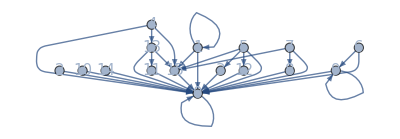

```mathematica
transitions = conditionTable[[All, 3]];
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.4,  DirectedEdges->True, ImageSize->Full, VertexLabelStyle -> 15]
```

```mathematica
(*Here will will get all graphs and their regions*)
(*We will initialise with the transitions from 0 and their regions*)
transitions = conditionTable[[All, 3]];
possible = Table[{transitions[[1]][[j]][[1]],transitions[[1]][[j]][[2]]},{j,1,Length[transitions[[1]]]}];
graphAssumptions = {1 > r > p > 0, t==1, s==0 && 1> epsilon > 0 };

Do[
(*Updated possible after adding the next round of transitions*)
next = {};
Do[
Do[
Print[i," ",j," ", k];
(*Add a new transition to possible[[k]]*)
function = Assuming[graphAssumptions,Simplify[And[possible[[k]][[2]],transitions[[i]][[j]][[2]]]]];
(*If the new region is non empty, add possible[[k]] with the new transition to next*)
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],transitions[[i]][[j]][[1]]}],Assuming[graphAssumptions,Simplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
,{j,1,Length[transitions[[i]]]}];
possible = next;
,{i,2,16}];        

(*Add the restrictions*)
Graphs = Table[{possible[[i]][[1]],Simplify[possible[[i]][[2]]&&( And @@ graphAssumptions)]},{i,1,Length[possible]}];

(*Delete regions which will now become empty*)
Graphs = DeleteCases[Graphs,{_,False}];
Print[Length[Graphs]];
Grid[Table[{i,Graphs[[i]][[1]],Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]

edgeslist = Graphs[[All,1]];
todraw = Graphs[[All,2]];
```

1 | {0→0,1→0,2→0,3→0,4→0,5→0,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&2 r≠1&&(2 (epsilon (-1+p)+r)<2 p+epsilon^2 (-1+p+r)||epsilon p+r<epsilon+p)&&(epsilon p+r≥epsilon+p||2+2 epsilon (-2+2 p+r)<4 p+epsilon^2 (-1+p+r))&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
2 | {0→0,1→0,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&r<p+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
3 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
4 | {0→0,1→0,2→0,3→0,4→0,5→12,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&2 r≠1&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)))&&t>r>p>s
5 | {0→0,1→0,2→0,3→0,4→13,5→12,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2 r≠1&&((2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&√2+epsilon<2)||(√2+epsilon>2&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)))&&t>r>p>s
6 | {0→0,1→0,2→0,3→0,4→0,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
7 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
8 | {0→0,1→0,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
9 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
10 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
11 | {0→0,1→0,2→0,3→0,4→0,5→0,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(2 (epsilon (-1+p)+r)<2 p+epsilon^2 (-1+p+r)||epsilon p+r<epsilon+p)&&(epsilon p+r≥epsilon+p||2+2 epsilon (-2+2 p+r)<4 p+epsilon^2 (-1+p+r))&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
12 | {0→0,1→0,2→0,3→0,4→0,5→3,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&r<p+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
13 | {0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
14 | {0→0,1→0,2→0,3→0,4→0,5→12,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)))&&t>r>p>s
15 | {0→0,1→0,2→0,3→0,4→13,5→12,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)))&&t>r>p>s
16 | {0→0,1→1,2→0,3→0,4→13,5→12,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&√2+epsilon<2&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
17 | {0→0,1→15,2→0,3→0,4→13,5→12,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&√2+epsilon<2&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
18 | {0→0,1→0,2→0,3→0,4→0,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
19 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
20 | {0→0,1→0,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
21 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
22 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 r≠1&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
23 | {0→0,1→0,2→0,3→0,4→0,5→0,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&(2 (epsilon (-1+p)+r)<2 p+epsilon^2 (-1+p+r)||epsilon p+r<epsilon+p)&&(epsilon p+r≥epsilon+p||2+2 epsilon (-2+2 p+r)<4 p+epsilon^2 (-1+p+r))&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
24 | {0→0,1→0,2→0,3→0,4→0,5→3,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&r<p+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
25 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
26 | {0→0,1→0,2→0,3→0,4→0,5→12,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)))&&t>r>p>s
27 | {0→0,1→0,2→0,3→0,4→13,5→12,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&((2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&√2+epsilon<2)||(√2+epsilon>2&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)))&&t>r>p>s
28 | {0→0,1→0,2→0,3→0,4→0,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
29 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
30 | {0→0,1→0,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
31 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
32 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
33 | {0→0,1→0,2→0,3→0,4→0,5→0,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon (-1+p)+r)<2 p+epsilon^2 (-1+p+r)||epsilon p+r<epsilon+p)&&(epsilon p+r≥epsilon+p||2+2 epsilon (-2+2 p+r)<4 p+epsilon^2 (-1+p+r))&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
34 | {0→0,1→0,2→0,3→0,4→0,5→3,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&r<p+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
35 | {0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
36 | {0→0,1→0,2→0,3→0,4→0,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)))&&t>r>p>s
37 | {0→0,1→1,2→0,3→0,4→0,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)))&&t>r>p>s
38 | {0→0,1→0,2→0,3→0,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&((√2+epsilon<2&&(((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)<1||r>p+epsilon r)&&(r≤p+epsilon r||2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)))||(√2+epsilon>2&&r>p+epsilon r&&((-2+epsilon) ((-2+epsilon) p+epsilon r))/(2-4 epsilon+epsilon^2)>1&&4 r+epsilon^2 (-1+p+r)<2+2 epsilon (-1+p+2 r)))&&t>r>p>s
39 | {0→0,1→1,2→0,3→0,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | √2+epsilon<2&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&t>r>p>s
40 | {0→0,1→15,2→0,3→0,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | √2+epsilon<2&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2+2 epsilon (-1+p+2 r)>4 r+epsilon^2 (-1+p+r)&&t>r>p>s
41 | {0→0,1→0,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
42 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2 epsilon p+r<epsilon+3 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
43 | {0→0,1→0,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&r<epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
44 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
45 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2+(2-2 epsilon+epsilon^2) p>epsilon+(-2+epsilon)^2 r&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
46 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
47 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
48 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
49 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
50 | {0→0,1→1,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
51 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
52 | {0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
53 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
54 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
55 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
56 | {0→0,1→1,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
57 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
58 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
59 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
60 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
61 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
62 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
63 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
64 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
65 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
66 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
67 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
68 | {0→0,1→1,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&2+epsilon^2+epsilon (-2+p+r)<2 r&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
69 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
70 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
71 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
72 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→15,8→0,9→0,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&t>r>p>s
73 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
74 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
75 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
76 | {0→0,1→1,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
77 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
78 | {0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&2 r≠1&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
79 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
80 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
81 | {0→0,1→1,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
82 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 r≠1&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
83 | {0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&r<p+epsilon r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2 (p-r)+epsilon^2 (-1+p+r)<2 epsilon (-1+p)&&2 r+epsilon^2 (p+r)<2 (epsilon+p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&t>r>p>s
84 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
85 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
86 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+epsilon^2+epsilon (-2+p+r)>2 r&&2 (-1+p)<epsilon (-4+epsilon+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
87 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
88 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
89 | {0→0,1→1,2→0,3→0,4→0,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
90 | {0→0,1→1,2→0,3→0,4→13,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
91 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
92 | {0→0,1→1,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
93 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
94 | {0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&2 epsilon p+r<epsilon+3 p&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&(1+epsilon (-2+p+r)<2 p||2 p>1)&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&t>r>p>s
95 | {0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&r>p+epsilon r&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
96 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
97 | {0→0,1→1,2→0,3→0,4→15,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&(2 (epsilon+p-r+epsilon r)<epsilon^2 (p+r)||r>p+epsilon r)&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&(2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)||r≤p+epsilon r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&epsilon+((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)<r<epsilon+3 p-2 epsilon p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&t>r>p>s
98 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0} | 3 p<r&&2+(2-2 epsilon+epsilon^2) p<epsilon+(-2+epsilon)^2 r&&epsilon p+2 r<1+(2 p)/epsilon+epsilon r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&t>r>p>s
99 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
100 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
101 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
102 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
103 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→8,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
104 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
105 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
106 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
107 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
108 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→15,8→0,9→0,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r>epsilon&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&t>r>p>s
109 | {0→0,1→15,2→0,3→0,4→13,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
110 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
111 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
112 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→0,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 2 r≠1&&3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&2 epsilon+p+r+√(8+p^2-8 r+2 p r+r^2)>4&&t>r>p>s
113 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 2 (-1+p)<epsilon (-4+epsilon+p+r)&&3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&2+epsilon^2+epsilon (-2+p+r)>2 r&&t>r>p>s
114 | {0→0,1→15,2→0,3→0,4→15,5→15,6→0,7→15,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))>5&&t>r>p>s
115 | {0→0,1→15,2→0,3→0,4→13,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&5+(4 r)/epsilon+epsilon (p+r)<2 (2/epsilon+epsilon+p+2 r)&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&1+epsilon (-2+p+r)>2 p&&t>r>p>s
116 | {0→0,1→15,2→0,3→0,4→15,5→15,6→9,7→15,8→0,9→9,10→0,11→0,12→0,13→15,14→0,15→0} | 3 p<r&&1+epsilon r<2 r&&2+(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r<epsilon&&epsilon+2 p+epsilon^2 (-p+r)<2 epsilon r&&2+epsilon^2+epsilon (-2+p+r)<2 r&&2+2 epsilon (-1+p+2 r)<4 r+epsilon^2 (-1+p+r)&&4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5&&r>p+epsilon r&&2 epsilon p+r>epsilon+3 p&&5+(4 r)/epsilon+epsilon (p+r)>2 (2/epsilon+epsilon+p+2 r)&&t>r>p>s

```mathematica
(*Define the conditions for all the 6 cases, as defined in the paper*)
(*Case1: Policy 1 (D,D,D,C) is the best response to itself.
Case2: Policy 9 (C,D,D,C) is the best response to itself.
Case3: Policy 9 (C,D,D,C) is the best response to policy 6 (D,C,C,D).*)
Case1 = (((-2+3 epsilon-2 epsilon^2) p)/(-2+epsilon)+epsilon <r<(3-2 epsilon) p+epsilon );
Case2 = (-3+2 epsilon) p<((-2+epsilon) ((-1+2 epsilon) r))/epsilon+1 &&(2-3 epsilon+2 epsilon^2) p+(-4+5 epsilon-2 epsilon^2) r+2<epsilon ;
Case3 = 4 epsilon+p+r+√(9+p^2-10 r+r^2+2 p (3+r))<5;

CaseA= Simplify[Case1 && !Case2 && r > p];
CaseB= Simplify[Case1 && Case2 && !Case3&& r > p];
CaseC= Simplify[Case1 && Case2 && Case3&& r > p];
CaseD= Simplify[!Case1 && Case2 && Case3&& r > p];
CaseE= Simplify[!Case1 && Case2 && !Case3&& r > p];
CaseF= Simplify[!Case1 && !Case2&& r > p];
CasesToDraw = {CaseA,CaseB,CaseC,CaseD,CaseE,CaseF};
```

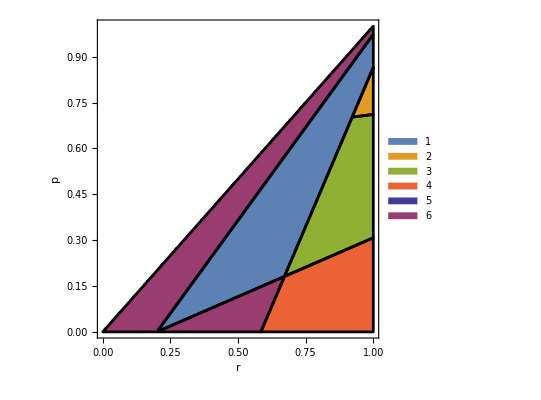

```mathematica
formulas = ReplaceAll[CasesToDraw, {epsilon->0.2,r-> x,p->y}];
regionplotSHd75=RegionPlot[formulas,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotStyle->{ColorData[97][1], ColorData[97][2], ColorData[97][3], ColorData[97][4], ColorData[1][1], ColorData[1][2]},BoundaryStyle->Black,PlotLegends->Placed[Automatic,{Left, Top}],PerformanceGoal->"Quality",FrameLabel->{"r","p"}, MaxRecursion->5]
```